## Non evaporating mathematical fluid, G=1/3, Bo=1/300

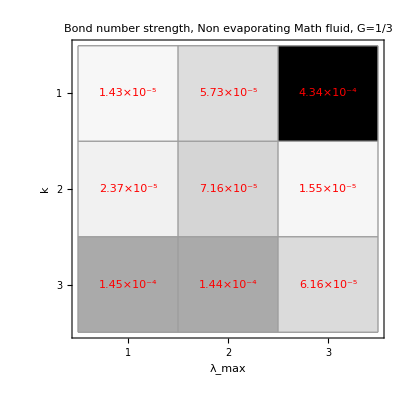

```mathematica
Gmat={{1.43*10^-5,5.73*10^-5,4.34*10^-4},{2.37*10^-5,7.16*10^-5,1.55*10^-5},{1.45*10^-4,1.44*10^-4,6.16*10^-5}};
ArrayPlot[Gmat,Epilog->{Red,MapIndexed[Text[#1//ScientificForm,Reverse[#2-0.5]]&,Reverse[Gmat],{2}]},Mesh->True,Frame->True,FrameTicks->{{1,2,3},{1,2,3}},FrameLabel->{"k","λ_max"},PlotLabel->"Bond number strength, Non evaporating Math fluid,
G=1/3"]
```

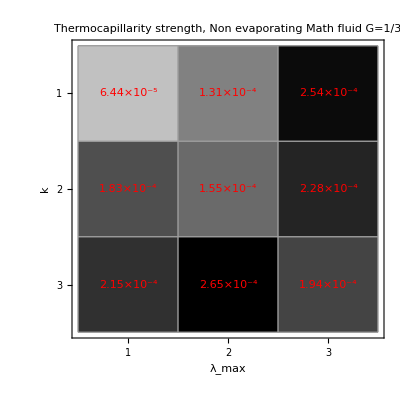

```mathematica
Mmat={{6.44*10^-5, 1.31*10^-4, 2.54*10^-4},{1.83*10^-4, 1.55*10^-4, 2.28*10^-4},{2.15*10^-4,2.65*10^-4,1.94*10^-4}};
ArrayPlot[Mmat,Epilog->{Red,MapIndexed[Text[#1//ScientificForm,Reverse[#2-0.5]]&,Reverse[Mmat],{2}]},Mesh->True,Frame->True,FrameTicks->{{1,2,3},{1,2,3}},FrameLabel->{"k","λ_max"},PlotLabel->"Thermocapillarity strength, Non evaporating Math fluid 
G=1/3"]
```

## Non evaporating mathematical fluid, G=0, Bo=0

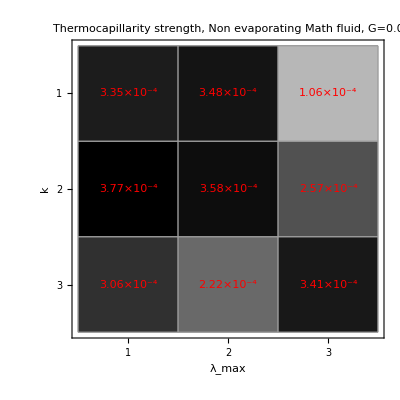

```mathematica
Mmat={{3.35*10^-4,3.48*10^-4,1.06*10^-4},{3.77*10^-4,3.58*10^-4,2.57*10^-4},{3.06*10^-4,2.22*10^-4,3.41*10^-4}};
ArrayPlot[Mmat,Epilog->{Red,MapIndexed[Text[#1//ScientificForm,Reverse[#2-0.5]]&,Reverse[Mmat],{2}]},Mesh->True,Frame->True,FrameTicks->{{1,2,3},{1,2,3}},FrameLabel->{"k","λ_max"},PlotLabel->"Thermocapillarity strength, Non evaporating Math fluid, 
G=0.0"]
```

## Evaporating mathematical fluid, G=1/3, Bo=1/300, E=0.0001

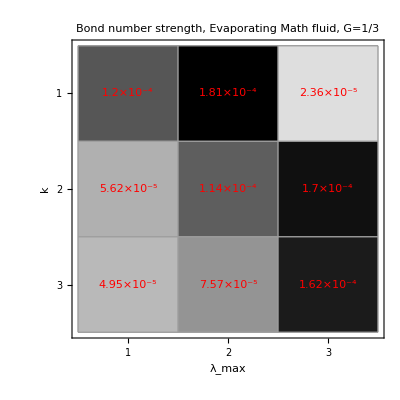

```mathematica
Gmat={{1.20*10^-4,1.81*10^-4,2.36*10^-5},{5.62*10^-5,1.14*10^-4,1.70*10^-4},{4.95*10^-5,7.57*10^-5,1.62*10^-4}};
ArrayPlot[Gmat,Epilog->{Red,MapIndexed[Text[#1//ScientificForm,Reverse[#2-0.5]]&,Reverse[Gmat],{2}]},Mesh->True,Frame->True,FrameTicks->{{1,2,3},{1,2,3}},FrameLabel->{"k","λ_max"},PlotLabel->"Bond number strength, Evaporating Math fluid,
G=1/3"]
```

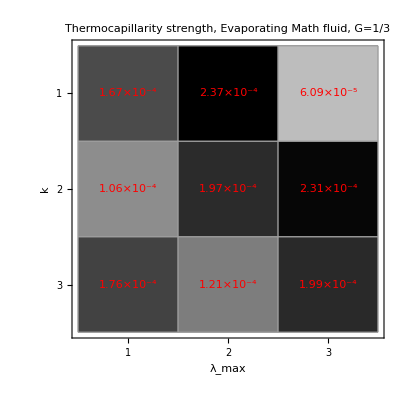

```mathematica
Mmat={{1.67*10^-4,2.37*10^-4,6.09*10^-5},{1.06*10^-4,1.97*10^-4,2.31*10^-4},{1.76*10^-4,1.21*10^-4,1.99*10^-4}};
ArrayPlot[Mmat,Epilog->{Red,MapIndexed[Text[#1//ScientificForm,Reverse[#2-0.5]]&,Reverse[Mmat],{2}]},Mesh->True,Frame->True,FrameTicks->{{1,2,3},{1,2,3}},FrameLabel->{"k","λ_max"},PlotLabel->"Thermocapillarity strength, Evaporating Math fluid, 
G=1/3"]
```

## Evaporating mathematical fluid, G=0, Bo=0, E=0.0001

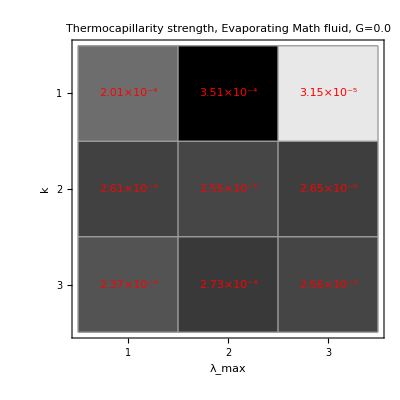

```mathematica
Mmat={{2.01*10^-4,3.51*10^-4,3.15*10^-5},{2.61*10^-4,2.55*10^-4,2.65*10^-4},{2.37*10^-4,2.73*10^-4,2.56*10^-4}};
ArrayPlot[Mmat,Epilog->{Red,MapIndexed[Text[#1//ScientificForm,Reverse[#2-0.5]]&,Reverse[Mmat],{2}]},Mesh->True,Frame->True,FrameTicks->{{1,2,3},{1,2,3}},FrameLabel->{"k","λ_max"},PlotLabel->"Thermocapillarity strength, Evaporating Math fluid, 
G=0.0"]
```

```mathematica
Evaporating mathematical fluid, G=0, Bo=0, E=0.0001. Comparison of S and M effects at IC and Rupture
```

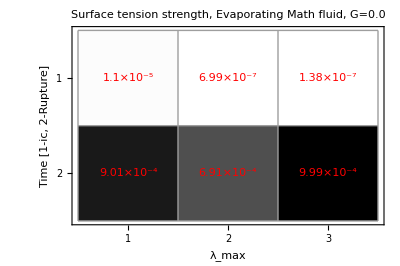

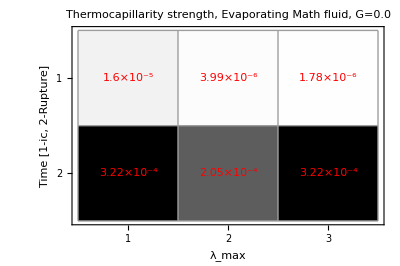

```mathematica
Smat={{1.1*10^-5,6.99*10^-7,1.38*10^-7},{9.01*10^-4,6.91*10^-4,9.99*10^-4}};
ArrayPlot[Smat,Epilog->{Red,MapIndexed[Text[#1//ScientificForm,Reverse[#2-0.5]]&,Reverse[Smat],{2}]},Mesh->True,Frame->True,FrameTicks->{{1,2},{1,2,3}},FrameLabel->{"Time [1-ic, 2-Rupture]","λ_max"},PlotLabel->"Surface tension strength, Evaporating Math fluid, 
G=0.0"]

Mmat={{1.6*10^-5,3.99*10^-6,1.78*10^-6},{3.22*10^-4,2.05*10^-4,3.22*10^-4}};
ArrayPlot[Mmat,Epilog->{Red,MapIndexed[Text[#1//ScientificForm,Reverse[#2-0.5]]&,Reverse[Mmat],{2}]},Mesh->True,Frame->True,FrameTicks->{{1,2},{1,2,3}},FrameLabel->{"Time [1-ic, 2-Rupture]","λ_max"},PlotLabel->"Thermocapillarity strength, Evaporating Math fluid, 
G=0.0"]
```

## Evaporating mathematical fluid, G = 0, Bo = 0, E = 0.0001. Comparison of S and M effects at different Initial condition amplitudes

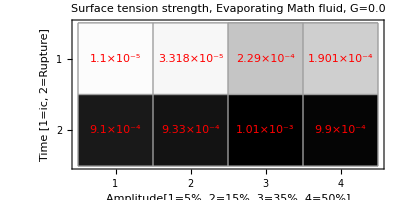

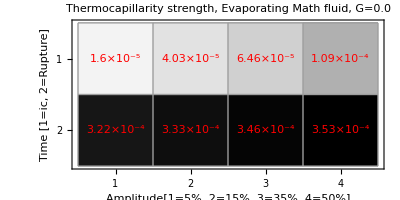

```mathematica
Smat={{1.1*10^-5,3.318*10^-5,2.29*10^-4,1.901*10^-4},{9.10*10^-4,9.33*10^-4,1.01*10^-3,9.9*10^-4}};
ArrayPlot[Smat,Epilog->{Red,MapIndexed[Text[#1//ScientificForm,Reverse[#2-0.5]]&,Reverse[Smat],{2}]},Mesh->True,Frame->True,FrameTicks->{{1,2},{1,2,3,4}},FrameLabel->{"Time [1=ic, 2=Rupture]","Amplitude[1=5%, 2=15%, 3=35%, 4=50%]"},PlotLabel->"Surface tension strength, Evaporating Math fluid, 
G=0.0"]

Mmat={{1.6*10^-5,4.03*10^-5,6.46*10^-5,1.09*10^-4},{3.22*10^-4,3.33*10^-4,3.46*10^-4,3.53*10^-4}};
ArrayPlot[Mmat,Epilog->{Red,MapIndexed[Text[#1//ScientificForm,Reverse[#2-0.5]]&,Reverse[Mmat],{2}]},Mesh->True,Frame->True,FrameTicks->{{1,2},{1,2,3,4}},FrameLabel->{"Time [1=ic, 2=Rupture]","Amplitude[1=5%, 2=15%, 3=35%, 4=50%]"},PlotLabel->"Thermocapillarity strength, Evaporating Math fluid, 
G=0.0"]
```